# CGA5_SampleFile

## 作成日:2014/10/23 最終更新日:2015/04/16

九州大学大学院　数理学府 修士２年　近藤 光浩,松尾 拓哉

パッケージを読み込むフォルダをSetDirectoryで指定しておく.

```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"Dropbox/Ymken2014/2014_M1seminar/20140424_Versor"}]];
<<CGA5Package`;
```

## 第一章 基本関数

## Basis

ℝ^(4,1) の基底をB={0, 1, 2, 3, ∞} とする.
𝔾^(4,1) の基底をGB={w[S] | S⊂ B}とする.
GBの元は (2^5 =) 32 個ある.
ℝ^3⊂ℝ^(4,1)⊂𝔾^(4,1) この包含写像を Inc:ℝ^3→ 𝔾^(4,1) とする.
点p∈ℝ^3に対して,Inc(p)=Pnt[p]である.
三点p,q,r∈ℝ^3を通るℝ^3内の円をCとするとき,Inc(C)=Cir[p,q,r]である.

### 例

```mathematica
Pnt[{1,2,3}]
```

w[{0}]+w[{1}]+2 w[{2}]+3 w[{3}]+7 w[{∞}]

```mathematica
Cir[{1,2,3},{2,8,3},{2,8,4}]
```

w[{0,1,3}]+7/2 w[{0,1,∞}]+6 w[{0,2,3}]+21 w[{0,2,∞}]-63/2 w[{0,3,∞}]+4 w[{1,2,3}]+14 w[{1,2,∞}]-35 w[{1,3,∞}]-84 w[{2,3,∞}]

### 和,差,スカラー倍

𝔾^(4,1) の和と差とスカラー倍は,線形空間ℝ^32と同様で記号は+と-を用いる.

```mathematica
Pnt[{1,2,3}]+Pnt[{6,5,4}]
```

2 w[{0}]+7 w[{1}]+7 w[{2}]+7 w[{3}]+91/2 w[{∞}]

```mathematica
Pnt[{1,2,3}]-Pnt[{1,0,3}]
```

2 w[{2}]+2 w[{∞}]

```mathematica
Pnt[{1,2,3}]
```

w[{0}]+w[{1}]+2 w[{2}]+3 w[{3}]+7 w[{∞}]

```mathematica
3Pnt[{1,2,3}]//Expand
```

3 w[{0}]+3 w[{1}]+6 w[{2}]+9 w[{3}]+21 w[{∞}]

## CGAProduct : 𝔾^(4,1)×𝔾^(4,1)→𝔾^(4,1) , (𝔾^(4,1))^n→𝔾^(4,1)(n≥0)

CGAの基本的な演算.
幾何積(Geometric Product,ジオメトリック積,CGA積:*)

CGAProduct は,幾何積を表す関数である.
引数には,CGAの元の組を用いる.

### 計算例

```mathematica
CGAProduct[ w[{∞}],w[{0}]]
```

-w[{}]-w[{0,∞}]

```mathematica
CGAProduct[w[{0}], w[{∞}]]
```

-w[{}]+w[{0,∞}]

```mathematica
CGAProduct[w[{0,∞}],w[{0,∞}]]
```

w[{}]

```mathematica
CGAProduct[w[{3,∞}],w[{3,∞}]]
```

0

```mathematica
CGAProduct[w[{0,∞}],w[{0}]]
```

-w[{0}]

```mathematica
CGAProduct[w[{0,∞}],w[{1,2,3}]]
```

-w[{0,1,2,3,∞}]

```mathematica
CGAProduct[w[{∞}],w[{0,∞}]]
```

-w[{∞}]

```mathematica
CGAProduct[w[{2,∞}],w[{2}]]
```

-w[{∞}]

```mathematica
CGAProduct[w[{2,3}],2w[{2,3}]]
```

-2 w[{}]

```mathematica
CGAProduct[w[{0,2}],w[{1,2,3}]]
```

-w[{0,1,3}]

```mathematica
CGAProduct[w[{0,1,2,3,∞}],w[{0,1,2,3,∞}]]
```

-w[{}]

```mathematica
CGAProduct[w[{0,1,2,∞}],w[{0,1,2,∞}]]
```

-w[{}]

```mathematica
w[{}]+CGAProduct[w[{∞}],w[{0}]]
```

-w[{0,∞}]

```mathematica
CGAProduct[(w[{}]+CGAProduct[w[{∞}],w[{0}]]) , (w[{}]+CGAProduct[w[{∞}],w[{0}]]) ]
```

w[{}]

線形性をもつ.

```mathematica
CGAProduct[ w[{0}]+3 w[{2}], 5 w[{3}]-7 w[{∞}]]
```

7 w[{}]+5 w[{0,3}]-7 w[{0,∞}]+15 w[{2,3}]-21 w[{2,∞}]

```mathematica
CGAProduct[ w[{0}], 5 w[{3}]-7 w[{∞}]]+3CGAProduct[ w[{2}], 5 w[{3}]-7 w[{∞}]]//Expand
```

7 w[{}]+5 w[{0,3}]-7 w[{0,∞}]+15 w[{2,3}]-21 w[{2,∞}]

```mathematica
CGAProduct[ w[{0,∞}],2 w[{0}]+3w[{1}]]
```

-2 w[{0}]-3 w[{0,1,∞}]

```mathematica
2 CGAProduct[ w[{0,∞}], w[{0}]]+3 CGAProduct[ w[{0,∞}],w[{1}]]
```

-2 w[{0}]-3 w[{0,1,∞}]

スカラー倍は w[{}] (またはSca)を用いて表現可能.

```mathematica
CGAProduct[w[{2,3}],3 w[{}] ]
```

3 w[{2,3}]

```mathematica
CGAProduct[3 w[{}],w[{2,3}] ]
```

3 w[{2,3}]

```mathematica
CGAProduct[w[{2,3}],Sca[3] ]
```

3 w[{2,3}]

### 引数が三つ以上の場合

{}でくくって,複数の元を引数に

```mathematica
CGAProduct[{ w[{2,3}], w[{0}], w[{0}] }]
```

0

```mathematica
CGAProduct[{ w[{0,3}], w[{0,∞}], w[{0}]+w[{1}]}]
```

-w[{0,1,3}]

```mathematica
CGAProduct[{ w[{0,3}], w[{0,∞}], w[{0}]+w[{1}],  5 w[{3}]-7 w[{∞}] }]
```

-5 w[{0,1}]-7 w[{1,3}]+7 w[{0,1,3,∞}]

```mathematica
CGAProduct[{7 w[{0,1,3,∞}],w[{0}] }]
```

-7 w[{0,1,3}]

```mathematica
CGAProduct[{ w[{0,3}], w[{0,∞}], w[{0}]+w[{1}], 5 w[{3}]-7 w[{∞}],w[{0}] }]
```

-14 w[{0,1,3}]

交換法則は成り立たない！

```mathematica
CGAProduct[{ w[{0,3}], w[{0,∞}], w[{0}]+w[{1}],w[{0}], 5 w[{3}]-7 w[{∞}] }]
```

0

引数0個は単位元.

```mathematica
CGAProduct[ {}]
```

w[{}]

### 𝔾^(4,1)の幾何積の演算表(32×32).

```mathematica
GB=Map[w, Subsets[{0,1,2,3,∞}(*基底*)]];(*全ての部分集合*)
Array[CGAProduct[GB[[#1]], GB[[#2]]]&,{Length[GB],Length[GB]}]//MatrixForm
```

(w[{}] | w[{0}] | w[{1}] | w[{2}] | w[{3}] | w[{∞}] | w[{0,1}] | w[{0,2}] | w[{0,3}] | w[{0,∞}] | w[{1,2}] | w[{1,3}] | w[{1,∞}] | w[{2,3}] | w[{2,∞}] | w[{3,∞}] | w[{0,1,2}] | w[{0,1,3}] | w[{0,1,∞}] | w[{0,2,3}] | w[{0,2,∞}] | w[{0,3,∞}] | w[{1,2,3}] | w[{1,2,∞}] | w[{1,3,∞}] | w[{2,3,∞}] | w[{0,1,2,3}] | w[{0,1,2,∞}] | w[{0,1,3,∞}] | w[{0,2,3,∞}] | w[{1,2,3,∞}] | w[{0,1,2,3,∞}]
w[{0}] | 0 | w[{0,1}] | w[{0,2}] | w[{0,3}] | -w[{}]+w[{0,∞}] | 0 | 0 | 0 | w[{0}] | w[{0,1,2}] | w[{0,1,3}] | w[{1}]+w[{0,1,∞}] | w[{0,2,3}] | w[{2}]+w[{0,2,∞}] | w[{3}]+w[{0,3,∞}] | 0 | 0 | -w[{0,1}] | 0 | -w[{0,2}] | -w[{0,3}] | w[{0,1,2,3}] | -w[{1,2}]+w[{0,1,2,∞}] | -w[{1,3}]+w[{0,1,3,∞}] | -w[{2,3}]+w[{0,2,3,∞}] | 0 | w[{0,1,2}] | w[{0,1,3}] | w[{0,2,3}] | w[{1,2,3}]+w[{0,1,2,3,∞}] | -w[{0,1,2,3}]
w[{1}] | -w[{0,1}] | w[{}] | w[{1,2}] | w[{1,3}] | w[{1,∞}] | -w[{0}] | -w[{0,1,2}] | -w[{0,1,3}] | -w[{0,1,∞}] | w[{2}] | w[{3}] | w[{∞}] | w[{1,2,3}] | w[{1,2,∞}] | w[{1,3,∞}] | -w[{0,2}] | -w[{0,3}] | -w[{0,∞}] | -w[{0,1,2,3}] | -w[{0,1,2,∞}] | -w[{0,1,3,∞}] | w[{2,3}] | w[{2,∞}] | w[{3,∞}] | w[{1,2,3,∞}] | -w[{0,2,3}] | -w[{0,2,∞}] | -w[{0,3,∞}] | -w[{0,1,2,3,∞}] | w[{2,3,∞}] | -w[{0,2,3,∞}]
w[{2}] | -w[{0,2}] | -w[{1,2}] | w[{}] | w[{2,3}] | w[{2,∞}] | w[{0,1,2}] | -w[{0}] | -w[{0,2,3}] | -w[{0,2,∞}] | -w[{1}] | -w[{1,2,3}] | -w[{1,2,∞}] | w[{3}] | w[{∞}] | w[{2,3,∞}] | w[{0,1}] | w[{0,1,2,3}] | w[{0,1,2,∞}] | -w[{0,3}] | -w[{0,∞}] | -w[{0,2,3,∞}] | -w[{1,3}] | -w[{1,∞}] | -w[{1,2,3,∞}] | w[{3,∞}] | w[{0,1,3}] | w[{0,1,∞}] | w[{0,1,2,3,∞}] | -w[{0,3,∞}] | -w[{1,3,∞}] | w[{0,1,3,∞}]
w[{3}] | -w[{0,3}] | -w[{1,3}] | -w[{2,3}] | w[{}] | w[{3,∞}] | w[{0,1,3}] | w[{0,2,3}] | -w[{0}] | -w[{0,3,∞}] | w[{1,2,3}] | -w[{1}] | -w[{1,3,∞}] | -w[{2}] | -w[{2,3,∞}] | w[{∞}] | -w[{0,1,2,3}] | w[{0,1}] | w[{0,1,3,∞}] | w[{0,2}] | w[{0,2,3,∞}] | -w[{0,∞}] | w[{1,2}] | w[{1,2,3,∞}] | -w[{1,∞}] | -w[{2,∞}] | -w[{0,1,2}] | -w[{0,1,2,3,∞}] | w[{0,1,∞}] | w[{0,2,∞}] | w[{1,2,∞}] | -w[{0,1,2,∞}]
w[{∞}] | -w[{}]-w[{0,∞}] | -w[{1,∞}] | -w[{2,∞}] | -w[{3,∞}] | 0 | -w[{1}]+w[{0,1,∞}] | -w[{2}]+w[{0,2,∞}] | -w[{3}]+w[{0,3,∞}] | -w[{∞}] | w[{1,2,∞}] | w[{1,3,∞}] | 0 | w[{2,3,∞}] | 0 | 0 | -w[{1,2}]-w[{0,1,2,∞}] | -w[{1,3}]-w[{0,1,3,∞}] | -w[{1,∞}] | -w[{2,3}]-w[{0,2,3,∞}] | -w[{2,∞}] | -w[{3,∞}] | -w[{1,2,3,∞}] | 0 | 0 | 0 | -w[{1,2,3}]+w[{0,1,2,3,∞}] | -w[{1,2,∞}] | -w[{1,3,∞}] | -w[{2,3,∞}] | 0 | -w[{1,2,3,∞}]
w[{0,1}] | 0 | w[{0}] | w[{0,1,2}] | w[{0,1,3}] | w[{1}]+w[{0,1,∞}] | 0 | 0 | 0 | w[{0,1}] | w[{0,2}] | w[{0,3}] | -w[{}]+w[{0,∞}] | w[{0,1,2,3}] | -w[{1,2}]+w[{0,1,2,∞}] | -w[{1,3}]+w[{0,1,3,∞}] | 0 | 0 | -w[{0}] | 0 | -w[{0,1,2}] | -w[{0,1,3}] | w[{0,2,3}] | w[{2}]+w[{0,2,∞}] | w[{3}]+w[{0,3,∞}] | w[{1,2,3}]+w[{0,1,2,3,∞}] | 0 | w[{0,2}] | w[{0,3}] | w[{0,1,2,3}] | -w[{2,3}]+w[{0,2,3,∞}] | -w[{0,2,3}]
w[{0,2}] | 0 | -w[{0,1,2}] | w[{0}] | w[{0,2,3}] | w[{2}]+w[{0,2,∞}] | 0 | 0 | 0 | w[{0,2}] | -w[{0,1}] | -w[{0,1,2,3}] | w[{1,2}]-w[{0,1,2,∞}] | w[{0,3}] | -w[{}]+w[{0,∞}] | -w[{2,3}]+w[{0,2,3,∞}] | 0 | 0 | w[{0,1,2}] | 0 | -w[{0}] | -w[{0,2,3}] | -w[{0,1,3}] | -w[{1}]-w[{0,1,∞}] | -w[{1,2,3}]-w[{0,1,2,3,∞}] | w[{3}]+w[{0,3,∞}] | 0 | -w[{0,1}] | -w[{0,1,2,3}] | w[{0,3}] | w[{1,3}]-w[{0,1,3,∞}] | w[{0,1,3}]
w[{0,3}] | 0 | -w[{0,1,3}] | -w[{0,2,3}] | w[{0}] | w[{3}]+w[{0,3,∞}] | 0 | 0 | 0 | w[{0,3}] | w[{0,1,2,3}] | -w[{0,1}] | w[{1,3}]-w[{0,1,3,∞}] | -w[{0,2}] | w[{2,3}]-w[{0,2,3,∞}] | -w[{}]+w[{0,∞}] | 0 | 0 | w[{0,1,3}] | 0 | w[{0,2,3}] | -w[{0}] | w[{0,1,2}] | w[{1,2,3}]+w[{0,1,2,3,∞}] | -w[{1}]-w[{0,1,∞}] | -w[{2}]-w[{0,2,∞}] | 0 | w[{0,1,2,3}] | -w[{0,1}] | -w[{0,2}] | -w[{1,2}]+w[{0,1,2,∞}] | -w[{0,1,2}]
w[{0,∞}] | -w[{0}] | -w[{0,1,∞}] | -w[{0,2,∞}] | -w[{0,3,∞}] | w[{∞}] | -w[{0,1}] | -w[{0,2}] | -w[{0,3}] | w[{}] | w[{0,1,2,∞}] | w[{0,1,3,∞}] | w[{1,∞}] | w[{0,2,3,∞}] | w[{2,∞}] | w[{3,∞}] | -w[{0,1,2}] | -w[{0,1,3}] | -w[{1}] | -w[{0,2,3}] | -w[{2}] | -w[{3}] | -w[{0,1,2,3,∞}] | w[{1,2,∞}] | w[{1,3,∞}] | w[{2,3,∞}] | -w[{0,1,2,3}] | w[{1,2}] | w[{1,3}] | w[{2,3}] | w[{1,2,3,∞}] | -w[{1,2,3}]
w[{1,2}] | w[{0,1,2}] | -w[{2}] | w[{1}] | w[{1,2,3}] | w[{1,2,∞}] | -w[{0,2}] | w[{0,1}] | w[{0,1,2,3}] | w[{0,1,2,∞}] | -w[{}] | -w[{2,3}] | -w[{2,∞}] | w[{1,3}] | w[{1,∞}] | w[{1,2,3,∞}] | -w[{0}] | -w[{0,2,3}] | -w[{0,2,∞}] | w[{0,1,3}] | w[{0,1,∞}] | w[{0,1,2,3,∞}] | -w[{3}] | -w[{∞}] | -w[{2,3,∞}] | w[{1,3,∞}] | -w[{0,3}] | -w[{0,∞}] | -w[{0,2,3,∞}] | w[{0,1,3,∞}] | -w[{3,∞}] | -w[{0,3,∞}]
w[{1,3}] | w[{0,1,3}] | -w[{3}] | -w[{1,2,3}] | w[{1}] | w[{1,3,∞}] | -w[{0,3}] | -w[{0,1,2,3}] | w[{0,1}] | w[{0,1,3,∞}] | w[{2,3}] | -w[{}] | -w[{3,∞}] | -w[{1,2}] | -w[{1,2,3,∞}] | w[{1,∞}] | w[{0,2,3}] | -w[{0}] | -w[{0,3,∞}] | -w[{0,1,2}] | -w[{0,1,2,3,∞}] | w[{0,1,∞}] | w[{2}] | w[{2,3,∞}] | -w[{∞}] | -w[{1,2,∞}] | w[{0,2}] | w[{0,2,3,∞}] | -w[{0,∞}] | -w[{0,1,2,∞}] | w[{2,∞}] | w[{0,2,∞}]
w[{1,∞}] | -w[{1}]+w[{0,1,∞}] | -w[{∞}] | -w[{1,2,∞}] | -w[{1,3,∞}] | 0 | -w[{}]-w[{0,∞}] | -w[{1,2}]-w[{0,1,2,∞}] | -w[{1,3}]-w[{0,1,3,∞}] | -w[{1,∞}] | w[{2,∞}] | w[{3,∞}] | 0 | w[{1,2,3,∞}] | 0 | 0 | -w[{2}]+w[{0,2,∞}] | -w[{3}]+w[{0,3,∞}] | -w[{∞}] | -w[{1,2,3}]+w[{0,1,2,3,∞}] | -w[{1,2,∞}] | -w[{1,3,∞}] | -w[{2,3,∞}] | 0 | 0 | 0 | -w[{2,3}]-w[{0,2,3,∞}] | -w[{2,∞}] | -w[{3,∞}] | -w[{1,2,3,∞}] | 0 | -w[{2,3,∞}]
w[{2,3}] | w[{0,2,3}] | w[{1,2,3}] | -w[{3}] | w[{2}] | w[{2,3,∞}] | w[{0,1,2,3}] | -w[{0,3}] | w[{0,2}] | w[{0,2,3,∞}] | -w[{1,3}] | w[{1,2}] | w[{1,2,3,∞}] | -w[{}] | -w[{3,∞}] | w[{2,∞}] | -w[{0,1,3}] | w[{0,1,2}] | w[{0,1,2,3,∞}] | -w[{0}] | -w[{0,3,∞}] | w[{0,2,∞}] | -w[{1}] | -w[{1,3,∞}] | w[{1,2,∞}] | -w[{∞}] | -w[{0,1}] | -w[{0,1,3,∞}] | w[{0,1,2,∞}] | -w[{0,∞}] | -w[{1,∞}] | -w[{0,1,∞}]
w[{2,∞}] | -w[{2}]+w[{0,2,∞}] | w[{1,2,∞}] | -w[{∞}] | -w[{2,3,∞}] | 0 | w[{1,2}]+w[{0,1,2,∞}] | -w[{}]-w[{0,∞}] | -w[{2,3}]-w[{0,2,3,∞}] | -w[{2,∞}] | -w[{1,∞}] | -w[{1,2,3,∞}] | 0 | w[{3,∞}] | 0 | 0 | w[{1}]-w[{0,1,∞}] | w[{1,2,3}]-w[{0,1,2,3,∞}] | w[{1,2,∞}] | -w[{3}]+w[{0,3,∞}] | -w[{∞}] | -w[{2,3,∞}] | w[{1,3,∞}] | 0 | 0 | 0 | w[{1,3}]+w[{0,1,3,∞}] | w[{1,∞}] | w[{1,2,3,∞}] | -w[{3,∞}] | 0 | w[{1,3,∞}]
w[{3,∞}] | -w[{3}]+w[{0,3,∞}] | w[{1,3,∞}] | w[{2,3,∞}] | -w[{∞}] | 0 | w[{1,3}]+w[{0,1,3,∞}] | w[{2,3}]+w[{0,2,3,∞}] | -w[{}]-w[{0,∞}] | -w[{3,∞}] | w[{1,2,3,∞}] | -w[{1,∞}] | 0 | -w[{2,∞}] | 0 | 0 | -w[{1,2,3}]+w[{0,1,2,3,∞}] | w[{1}]-w[{0,1,∞}] | w[{1,3,∞}] | w[{2}]-w[{0,2,∞}] | w[{2,3,∞}] | -w[{∞}] | -w[{1,2,∞}] | 0 | 0 | 0 | -w[{1,2}]-w[{0,1,2,∞}] | -w[{1,2,3,∞}] | w[{1,∞}] | w[{2,∞}] | 0 | -w[{1,2,∞}]
w[{0,1,2}] | 0 | -w[{0,2}] | w[{0,1}] | w[{0,1,2,3}] | -w[{1,2}]+w[{0,1,2,∞}] | 0 | 0 | 0 | w[{0,1,2}] | -w[{0}] | -w[{0,2,3}] | -w[{2}]-w[{0,2,∞}] | w[{0,1,3}] | w[{1}]+w[{0,1,∞}] | w[{1,2,3}]+w[{0,1,2,3,∞}] | 0 | 0 | w[{0,2}] | 0 | -w[{0,1}] | -w[{0,1,2,3}] | -w[{0,3}] | w[{}]-w[{0,∞}] | w[{2,3}]-w[{0,2,3,∞}] | -w[{1,3}]+w[{0,1,3,∞}] | 0 | -w[{0}] | -w[{0,2,3}] | w[{0,1,3}] | -w[{3}]-w[{0,3,∞}] | w[{0,3}]
w[{0,1,3}] | 0 | -w[{0,3}] | -w[{0,1,2,3}] | w[{0,1}] | -w[{1,3}]+w[{0,1,3,∞}] | 0 | 0 | 0 | w[{0,1,3}] | w[{0,2,3}] | -w[{0}] | -w[{3}]-w[{0,3,∞}] | -w[{0,1,2}] | -w[{1,2,3}]-w[{0,1,2,3,∞}] | w[{1}]+w[{0,1,∞}] | 0 | 0 | w[{0,3}] | 0 | w[{0,1,2,3}] | -w[{0,1}] | w[{0,2}] | -w[{2,3}]+w[{0,2,3,∞}] | w[{}]-w[{0,∞}] | w[{1,2}]-w[{0,1,2,∞}] | 0 | w[{0,2,3}] | -w[{0}] | -w[{0,1,2}] | w[{2}]+w[{0,2,∞}] | -w[{0,2}]
w[{0,1,∞}] | -w[{0,1}] | -w[{0,∞}] | -w[{0,1,2,∞}] | -w[{0,1,3,∞}] | -w[{1,∞}] | -w[{0}] | -w[{0,1,2}] | -w[{0,1,3}] | -w[{1}] | w[{0,2,∞}] | w[{0,3,∞}] | -w[{∞}] | w[{0,1,2,3,∞}] | -w[{1,2,∞}] | -w[{1,3,∞}] | -w[{0,2}] | -w[{0,3}] | w[{}] | -w[{0,1,2,3}] | w[{1,2}] | w[{1,3}] | -w[{0,2,3,∞}] | -w[{2,∞}] | -w[{3,∞}] | -w[{1,2,3,∞}] | -w[{0,2,3}] | -w[{2}] | -w[{3}] | -w[{1,2,3}] | -w[{2,3,∞}] | w[{2,3}]
w[{0,2,3}] | 0 | w[{0,1,2,3}] | -w[{0,3}] | w[{0,2}] | -w[{2,3}]+w[{0,2,3,∞}] | 0 | 0 | 0 | w[{0,2,3}] | -w[{0,1,3}] | w[{0,1,2}] | w[{1,2,3}]+w[{0,1,2,3,∞}] | -w[{0}] | -w[{3}]-w[{0,3,∞}] | w[{2}]+w[{0,2,∞}] | 0 | 0 | -w[{0,1,2,3}] | 0 | w[{0,3}] | -w[{0,2}] | -w[{0,1}] | w[{1,3}]-w[{0,1,3,∞}] | -w[{1,2}]+w[{0,1,2,∞}] | w[{}]-w[{0,∞}] | 0 | -w[{0,1,3}] | w[{0,1,2}] | -w[{0}] | -w[{1}]-w[{0,1,∞}] | w[{0,1}]
w[{0,2,∞}] | -w[{0,2}] | w[{0,1,2,∞}] | -w[{0,∞}] | -w[{0,2,3,∞}] | -w[{2,∞}] | w[{0,1,2}] | -w[{0}] | -w[{0,2,3}] | -w[{2}] | -w[{0,1,∞}] | -w[{0,1,2,3,∞}] | w[{1,2,∞}] | w[{0,3,∞}] | -w[{∞}] | -w[{2,3,∞}] | w[{0,1}] | w[{0,1,2,3}] | -w[{1,2}] | -w[{0,3}] | w[{}] | w[{2,3}] | w[{0,1,3,∞}] | w[{1,∞}] | w[{1,2,3,∞}] | -w[{3,∞}] | w[{0,1,3}] | w[{1}] | w[{1,2,3}] | -w[{3}] | w[{1,3,∞}] | -w[{1,3}]
w[{0,3,∞}] | -w[{0,3}] | w[{0,1,3,∞}] | w[{0,2,3,∞}] | -w[{0,∞}] | -w[{3,∞}] | w[{0,1,3}] | w[{0,2,3}] | -w[{0}] | -w[{3}] | w[{0,1,2,3,∞}] | -w[{0,1,∞}] | w[{1,3,∞}] | -w[{0,2,∞}] | w[{2,3,∞}] | -w[{∞}] | -w[{0,1,2,3}] | w[{0,1}] | -w[{1,3}] | w[{0,2}] | -w[{2,3}] | w[{}] | -w[{0,1,2,∞}] | -w[{1,2,3,∞}] | w[{1,∞}] | w[{2,∞}] | -w[{0,1,2}] | -w[{1,2,3}] | w[{1}] | w[{2}] | -w[{1,2,∞}] | w[{1,2}]
w[{1,2,3}] | -w[{0,1,2,3}] | w[{2,3}] | -w[{1,3}] | w[{1,2}] | w[{1,2,3,∞}] | -w[{0,2,3}] | w[{0,1,3}] | -w[{0,1,2}] | -w[{0,1,2,3,∞}] | -w[{3}] | w[{2}] | w[{2,3,∞}] | -w[{1}] | -w[{1,3,∞}] | w[{1,2,∞}] | w[{0,3}] | -w[{0,2}] | -w[{0,2,3,∞}] | w[{0,1}] | w[{0,1,3,∞}] | -w[{0,1,2,∞}] | -w[{}] | -w[{3,∞}] | w[{2,∞}] | -w[{1,∞}] | w[{0}] | w[{0,3,∞}] | -w[{0,2,∞}] | w[{0,1,∞}] | -w[{∞}] | w[{0,∞}]
w[{1,2,∞}] | -w[{1,2}]-w[{0,1,2,∞}] | w[{2,∞}] | -w[{1,∞}] | -w[{1,2,3,∞}] | 0 | w[{2}]-w[{0,2,∞}] | -w[{1}]+w[{0,1,∞}] | -w[{1,2,3}]+w[{0,1,2,3,∞}] | -w[{1,2,∞}] | -w[{∞}] | -w[{2,3,∞}] | 0 | w[{1,3,∞}] | 0 | 0 | w[{}]+w[{0,∞}] | w[{2,3}]+w[{0,2,3,∞}] | w[{2,∞}] | -w[{1,3}]-w[{0,1,3,∞}] | -w[{1,∞}] | -w[{1,2,3,∞}] | w[{3,∞}] | 0 | 0 | 0 | w[{3}]-w[{0,3,∞}] | w[{∞}] | w[{2,3,∞}] | -w[{1,3,∞}] | 0 | w[{3,∞}]
w[{1,3,∞}] | -w[{1,3}]-w[{0,1,3,∞}] | w[{3,∞}] | w[{1,2,3,∞}] | -w[{1,∞}] | 0 | w[{3}]-w[{0,3,∞}] | w[{1,2,3}]-w[{0,1,2,3,∞}] | -w[{1}]+w[{0,1,∞}] | -w[{1,3,∞}] | w[{2,3,∞}] | -w[{∞}] | 0 | -w[{1,2,∞}] | 0 | 0 | -w[{2,3}]-w[{0,2,3,∞}] | w[{}]+w[{0,∞}] | w[{3,∞}] | w[{1,2}]+w[{0,1,2,∞}] | w[{1,2,3,∞}] | -w[{1,∞}] | -w[{2,∞}] | 0 | 0 | 0 | -w[{2}]+w[{0,2,∞}] | -w[{2,3,∞}] | w[{∞}] | w[{1,2,∞}] | 0 | -w[{2,∞}]
w[{2,3,∞}] | -w[{2,3}]-w[{0,2,3,∞}] | -w[{1,2,3,∞}] | w[{3,∞}] | -w[{2,∞}] | 0 | -w[{1,2,3}]+w[{0,1,2,3,∞}] | w[{3}]-w[{0,3,∞}] | -w[{2}]+w[{0,2,∞}] | -w[{2,3,∞}] | -w[{1,3,∞}] | w[{1,2,∞}] | 0 | -w[{∞}] | 0 | 0 | w[{1,3}]+w[{0,1,3,∞}] | -w[{1,2}]-w[{0,1,2,∞}] | -w[{1,2,3,∞}] | w[{}]+w[{0,∞}] | w[{3,∞}] | -w[{2,∞}] | w[{1,∞}] | 0 | 0 | 0 | w[{1}]-w[{0,1,∞}] | w[{1,3,∞}] | -w[{1,2,∞}] | w[{∞}] | 0 | w[{1,∞}]
w[{0,1,2,3}] | 0 | w[{0,2,3}] | -w[{0,1,3}] | w[{0,1,2}] | w[{1,2,3}]+w[{0,1,2,3,∞}] | 0 | 0 | 0 | w[{0,1,2,3}] | -w[{0,3}] | w[{0,2}] | -w[{2,3}]+w[{0,2,3,∞}] | -w[{0,1}] | w[{1,3}]-w[{0,1,3,∞}] | -w[{1,2}]+w[{0,1,2,∞}] | 0 | 0 | -w[{0,2,3}] | 0 | w[{0,1,3}] | -w[{0,1,2}] | -w[{0}] | -w[{3}]-w[{0,3,∞}] | w[{2}]+w[{0,2,∞}] | -w[{1}]-w[{0,1,∞}] | 0 | -w[{0,3}] | w[{0,2}] | -w[{0,1}] | w[{}]-w[{0,∞}] | w[{0}]
w[{0,1,2,∞}] | -w[{0,1,2}] | w[{0,2,∞}] | -w[{0,1,∞}] | -w[{0,1,2,3,∞}] | w[{1,2,∞}] | w[{0,2}] | -w[{0,1}] | -w[{0,1,2,3}] | w[{1,2}] | -w[{0,∞}] | -w[{0,2,3,∞}] | -w[{2,∞}] | w[{0,1,3,∞}] | w[{1,∞}] | w[{1,2,3,∞}] | w[{0}] | w[{0,2,3}] | w[{2}] | -w[{0,1,3}] | -w[{1}] | -w[{1,2,3}] | w[{0,3,∞}] | -w[{∞}] | -w[{2,3,∞}] | w[{1,3,∞}] | w[{0,3}] | -w[{}] | -w[{2,3}] | w[{1,3}] | -w[{3,∞}] | w[{3}]
w[{0,1,3,∞}] | -w[{0,1,3}] | w[{0,3,∞}] | w[{0,1,2,3,∞}] | -w[{0,1,∞}] | w[{1,3,∞}] | w[{0,3}] | w[{0,1,2,3}] | -w[{0,1}] | w[{1,3}] | w[{0,2,3,∞}] | -w[{0,∞}] | -w[{3,∞}] | -w[{0,1,2,∞}] | -w[{1,2,3,∞}] | w[{1,∞}] | -w[{0,2,3}] | w[{0}] | w[{3}] | w[{0,1,2}] | w[{1,2,3}] | -w[{1}] | -w[{0,2,∞}] | w[{2,3,∞}] | -w[{∞}] | -w[{1,2,∞}] | -w[{0,2}] | w[{2,3}] | -w[{}] | -w[{1,2}] | w[{2,∞}] | -w[{2}]
w[{0,2,3,∞}] | -w[{0,2,3}] | -w[{0,1,2,3,∞}] | w[{0,3,∞}] | -w[{0,2,∞}] | w[{2,3,∞}] | -w[{0,1,2,3}] | w[{0,3}] | -w[{0,2}] | w[{2,3}] | -w[{0,1,3,∞}] | w[{0,1,2,∞}] | w[{1,2,3,∞}] | -w[{0,∞}] | -w[{3,∞}] | w[{2,∞}] | w[{0,1,3}] | -w[{0,1,2}] | -w[{1,2,3}] | w[{0}] | w[{3}] | -w[{2}] | w[{0,1,∞}] | -w[{1,3,∞}] | w[{1,2,∞}] | -w[{∞}] | w[{0,1}] | -w[{1,3}] | w[{1,2}] | -w[{}] | -w[{1,∞}] | w[{1}]
w[{1,2,3,∞}] | -w[{1,2,3}]+w[{0,1,2,3,∞}] | -w[{2,3,∞}] | w[{1,3,∞}] | -w[{1,2,∞}] | 0 | -w[{2,3}]-w[{0,2,3,∞}] | w[{1,3}]+w[{0,1,3,∞}] | -w[{1,2}]-w[{0,1,2,∞}] | -w[{1,2,3,∞}] | -w[{3,∞}] | w[{2,∞}] | 0 | -w[{1,∞}] | 0 | 0 | w[{3}]-w[{0,3,∞}] | -w[{2}]+w[{0,2,∞}] | -w[{2,3,∞}] | w[{1}]-w[{0,1,∞}] | w[{1,3,∞}] | -w[{1,2,∞}] | w[{∞}] | 0 | 0 | 0 | w[{}]+w[{0,∞}] | w[{3,∞}] | -w[{2,∞}] | w[{1,∞}] | 0 | w[{∞}]
w[{0,1,2,3,∞}] | -w[{0,1,2,3}] | -w[{0,2,3,∞}] | w[{0,1,3,∞}] | -w[{0,1,2,∞}] | -w[{1,2,3,∞}] | -w[{0,2,3}] | w[{0,1,3}] | -w[{0,1,2}] | -w[{1,2,3}] | -w[{0,3,∞}] | w[{0,2,∞}] | -w[{2,3,∞}] | -w[{0,1,∞}] | w[{1,3,∞}] | -w[{1,2,∞}] | w[{0,3}] | -w[{0,2}] | w[{2,3}] | w[{0,1}] | -w[{1,3}] | w[{1,2}] | w[{0,∞}] | w[{3,∞}] | -w[{2,∞}] | w[{1,∞}] | w[{0}] | w[{3}] | -w[{2}] | w[{1}] | w[{∞}] | -w[{}])

## OuterProduct : 𝔾^(4,1)×𝔾^(4,1)→𝔾^(4,1) , (𝔾^(4,1))^n→𝔾^(4,1)(n≥0)

CGAの外積(ウェッジ積,楔積:^)
Blade同士の積の最大のGradeが外積となっている.

OuterProduct は,外積を表す関数である.
引数には,CGAの元の組を用いる.

### 計算例

```mathematica
OuterProduct[ w[{1}],w[{0}] ]
```

-w[{0,1}]

```mathematica
OuterProduct[ w[{2,∞}],w[{0,3}]]
```

-w[{0,2,3,∞}]

```mathematica
OuterProduct[w[{1,3}],w[{0}]]+OuterProduct[w[{2}],w[{0}]]
```

-w[{0,2}]+w[{0,1,3}]

```mathematica
OuterProduct[ 2w[{}],3 w[{}] ]
```

6 w[{}]

```mathematica
OuterProduct[w[{0,1,3}],0]
```

0

同じ元同士の外積は0

```mathematica
OuterProduct[w[{1,3}],w[{1,3}]]
```

0

反対称性

```mathematica
OuterProduct[ w[{∞}],w[{0}]]
```

-w[{0,∞}]

```mathematica
OuterProduct[ w[{0}],w[{∞}]]
```

w[{0,∞}]

線形性(分配則)

```mathematica
OuterProduct[w[{1,3}]+w[{2}],w[{0}]]
```

-w[{0,2}]+w[{0,1,3}]

```mathematica
OuterProduct[w[{1,3}],w[{0}]]+OuterProduct[w[{2}],w[{0}]]
```

-w[{0,2}]+w[{0,1,3}]

結合則

```mathematica
OuterProduct[  OuterProduct[w[{0}],w[{∞}]] , w[{3}]  ]
```

-w[{0,3,∞}]

```mathematica
OuterProduct[  w[{0}] , OuterProduct[w[{∞}],w[{3}]]  ]
```

-w[{0,3,∞}]

### 引数が三つ以上の場合

{}でくくって,複数の元を引数に

```mathematica
OuterProduct[{ w[{2,3}], w[{0}]+w[{∞}], w[{1}] }]
```

w[{0,1,2,3}]-w[{1,2,3,∞}]

```mathematica
OuterProduct[{ w[{0,3}]+w[{3}], w[{0,∞}]+5w[{2}]+3w[{0}], w[{1}]+w[{2}], 5 w[{3}]-7 w[{∞}] }]
```

-21 w[{0,1,3,∞}]-21 w[{0,2,3,∞}]+35 w[{1,2,3,∞}]+35 w[{0,1,2,3,∞}]

```mathematica
OuterProduct[{w[{0,3}], w[{0,∞}], w[{0}]+w[{1}],w[{0}], 5 w[{3}]-7 w[{∞}] }]
```

0

## InnerProduct : 𝔾^(4,1)×𝔾^(4,1)→𝔾^(4,1) , (𝔾^(4,1))^n→𝔾^(4,1)(n≥0)

CGAの内積(ドット積:・)
Blade同士の積の最小のGradeが内積となっている.

InnerProduct は,内積を表す関数である.
引数には,CGAの元の組を用いる.

### 計算例

```mathematica
InnerProduct[ w[{1}],w[{1}]]
```

w[{}]

```mathematica
InnerProduct[ w[{1}],w[{2}]]
```

0

```mathematica
InnerProduct[ w[{∞}],w[{0}]]
```

-w[{}]

```mathematica
InnerProduct[ w[{0,∞}],w[{∞}]]
```

w[{∞}]

```mathematica
InnerProduct[ w[{∞}],w[{0,∞}]]
```

-w[{∞}]

```mathematica
InnerProduct[ w[{0,∞}],w[{0}]]
```

-w[{0}]

```mathematica
InnerProduct[ w[{0,∞}],w[{0,∞}]]
```

w[{}]

```mathematica
InnerProduct[ w[{∞}],w[{∞}]]
```

0

```mathematica
InnerProduct[ 2w[{}],3 w[{}] ]
```

6 w[{}]

```mathematica
InnerProduct[w[{0,1,3}],0]
```

0

```mathematica
InnerProduct[w[{1,3}],w[{1,3}]]
```

-w[{}]

```mathematica
InnerProduct[ 5w[{1,3}]+2w[{0,1}]  ,7 w[{1}]]
```

14 w[{0}]-35 w[{3}]

```mathematica
InnerProduct[ 7w[{1}] , 5w[{1,3}]+2w[{0,1}] ]
```

-14 w[{0}]+35 w[{3}]

線形性

```mathematica
InnerProduct[ 5w[{1,3}]+2w[{0,1}] ,7w[{1}]]
```

14 w[{0}]-35 w[{3}]

```mathematica
InnerProduct[5w[{1,3}],7w[{1}]]+InnerProduct[2w[{0,1}],7w[{1}]]
```

14 w[{0}]-35 w[{3}]

### 引数が三つ以上の場合

{}でくくって,複数の元を引数に

```mathematica
InnerProduct[{ w[{2}], w[{1,2}]+w[{1,∞}], w[{1,2,3}] }]
```

-w[{2,3}]

## Reversion : 𝔾^(4,1)→𝔾^(4,1)

CGAの元の逆順

Reversion は,逆順を表す関数である.
引数には,CGAの元を用いる.

### 計算例

```mathematica
Reversion[w[{1}]]
```

w[{1}]

```mathematica
Reversion[w[{0,1}]]
```

-w[{0,1}]

```mathematica
Reversion[w[{1,2,3}]]
```

-w[{1,2,3}]

```mathematica
Reversion[w[{0,1,2,3}]]
```

w[{0,1,2,3}]

```mathematica
Reversion[w[{0,1,∞}]+w[{0,1,2,3}]]
```

-w[{0,1,∞}]+w[{0,1,2,3}]

## Dual : 𝔾^(4,1)→𝔾^(4,1)

CGAの元の双対

Dual は,双対を表す関数である.
引数には,CGAの元を用いる.

### 計算例

```mathematica
Dual[w[{∞}]]
```

w[{1,2,3,∞}]

```mathematica
Dual[w[{1}]]
```

w[{0,2,3,∞}]

```mathematica
Dual[w[{2}]]
```

-w[{0,1,3,∞}]

```mathematica
Dual[w[{0,1}]]
```

w[{0,2,3}]

```mathematica
Dual[w[{0,∞}]]
```

w[{1,2,3}]

```mathematica
Dual[w[{1,2,3}]]
```

-w[{0,∞}]

```mathematica
Dual[w[{0,1,2,3}]]
```

-w[{0}]

```mathematica
Dual[w[{0,1,∞}]+w[{0,1,2,3}]]
```

-w[{0}]-w[{2,3}]

## BASIC ELEMENTS

### ELEMENTS

CGAでの,ベクトル関係の元.

#### Sca : ℝ→𝔾^(4,1)

Sca は,スカラー(Scalar)を表す関数である.
引数には,実数を用いる.

```mathematica
Sca[8]
```

8 w[{}]

```mathematica
Sca[.2]
```

0.2 w[{}]

#### Vec : ℝ^3→𝔾^(4,1)

Vec は,ベクトル(Vector)を表す関数である.
引数には,実数の組を用いる.

```mathematica
Vec[{x,y,z}]
```

x w[{1}]+y w[{2}]+z w[{3}]

#### Biv : ℝ^3×ℝ^3→𝔾^(4,1)

Biv は,二重ベクトル(Bivector)を表す関数である.
引数には,実数の組を二つ用いる.

```mathematica
Biv[{0,1,0},{1,0,0}]
```

-w[{1,2}]

#### Tri : ℝ^3×ℝ^3×ℝ^3→𝔾^(4,1)

Tri は,三重ベクトル(Trivector)を表す関数である.
引数には,実数の組を三つ用いる.

```mathematica
Tri[{0,1,2},{1,0,2},{1,2,3}]
```

3 w[{1,2,3}]

### Round

CGAでの,球関係の元.

#### Pnt : ℝ^3→𝔾^(4,1)

Pnt は,点(Point)を表す関数である.
引数には,実数の組を用いる.

```mathematica
Pnt[{2,4,8}]
```

w[{0}]+2 w[{1}]+4 w[{2}]+8 w[{3}]+42 w[{∞}]

NPnt : Pnt[ℝ^3] → Pnt[ℝ^3]

NPnt は,点を正規化する関数である.
引数には,CGAの点を用いる.

```mathematica
D0=Dilator[Pnt[{1,2,0}],3]
```

w[{0}]/ⅇ^3+w[{1}]+2 w[{2}]+5/2 ⅇ^3 w[{∞}]

```mathematica
NPnt[Dilator[Pnt[{1,2,0}],3]]
```

w[{0}]+ⅇ^3 w[{1}]+2 ⅇ^3 w[{2}]+5/2 ⅇ^6 w[{∞}]

#### Par : ℝ^3×ℝ^3→𝔾^(4,1)

Par は,点対(PointPair)を表す関数である.
引数には,実数の組を二つ用いる.

```mathematica
Par[{6,1,4},{2,1,-2}]
```

-4 w[{0,1}]-6 w[{0,3}]-22 w[{0,∞}]+4 w[{1,2}]-20 w[{1,3}]-26 w[{1,∞}]-6 w[{2,3}]-22 w[{2,∞}]+71 w[{3,∞}]

#### Cir : ℝ^3×ℝ^3×ℝ^3→𝔾^(4,1)

Cir は,円(Circle)を表す関数である.
引数には,実数の組を三つ用いる.

```mathematica
Cir[{3,0,0},{0,3,0},{-3,0,0}]
```

18 w[{0,1,2}]+81 w[{1,2,∞}]

#### Sph : ℝ^3×ℝ^3×ℝ^3×ℝ^3→𝔾^(4,1)

Cir は,球(Sphere)を表す関数である.
引数には,実数の組を三つ用いる.

```mathematica
Sph[{3,0,0},{0,3,0},{0,0,3},{-3,0,0}]
```

-54 w[{0,1,2,3}]+243 w[{1,2,3,∞}]

### Flat

CGAでの,平面関係の元.

#### Lin : ℝ^3×ℝ^3→𝔾^(4,1)

Lin は,直線(Line)を表す関数である.
引数には,実数の組を二つ用いる.

```mathematica
Lin[{0,0,0},{2,5,0}]
```

2 w[{0,1,∞}]+5 w[{0,2,∞}]

#### Dll : ℝ^3×ℝ^3×ℝ^3→𝔾^(4,1)

Dllは,双対直線(DualLine)を表す関数である.
引数には,実数の組を二つと実数の組一つを用いる.

```mathematica
Dll[{0,1,2},{1,0,2},{1,2,3}]
```

-w[{1,2}]-2 w[{1,3}]+w[{1,∞}]+2 w[{2,3}]+2 w[{2,∞}]+3 w[{3,∞}]

#### Pln : ℝ^3×ℝ^3×ℝ^3→𝔾^(4,1)

Plnは,平面(Plane)を表す関数である.
引数には,実数の組を三つ用いる.

```mathematica
Pln[{3,0,1},{0,3,1},{0,2,1}]
```

3 w[{0,1,2,∞}]+3 w[{1,2,3,∞}]

#### Dlp : ℝ^3×ℝ→𝔾^(4,1)

Dlpは,双対平面(DualPlane)を表す関数である.
引数には,実数の組とスカラーを用いる.

```mathematica
Dlp[{3,8,1},9]
```

3 w[{1}]+8 w[{2}]+w[{3}]+9 w[{∞}]

#### Flp : ℝ^3→𝔾^(4,1)

Flp は,水平点(FlatPoint)を表す関数である.
引数には,実数の組を用いる.

Flp[p] = Pnt[p] ^ w[{∞}]]  ( p∈ℝ^3 )
ポイントペアの一点を無限大にとばしたもの.

```mathematica
Flp[{2,3,7}]
```

w[{0,∞}]+2 w[{1,∞}]+3 w[{2,∞}]+7 w[{3,∞}]

### Versors

CGAでの運動,作用.

#### Rotor : Pnt[ℝ^3]×Biv[ℝ^3×ℝ^3]×ℝ →𝔾^(4,1)

Rotorは,回転を表す関数である.
引数には,CGAの元と二重ベクトルとスカラーを用いる.

```mathematica
Rotor[Pnt[{1,0,0}],Biv[{1,0,0},{0,1,0}],θ]
```

w[{0}]+Cos[θ] w[{1}]+Sin[θ] w[{2}]+1/2 w[{∞}]

#### Translator : Pnt[ℝ^3]×Vec[ℝ^3] →𝔾^(4,1)

Translatorは,平行移動を表す関数である.
引数には,CGAの元とベクトルを用いる.

```mathematica
Translator[Pnt[{x,0,0}],Vec[{t,0,0}]]
```

w[{0}]+(t+x) w[{1}]+1/2 (t+x)^2 w[{∞}]

#### Dilator : Pnt[ℝ^3]×ℝ →𝔾^(4,1)

Dilatorは,拡大縮小を表す関数である.
引数には,CGAの元とスカラーを用いる.

```mathematica
Dilator[Pnt[{1,2,0}],3]
```

w[{0}]/ⅇ^3+w[{1}]+2 w[{2}]+5/2 ⅇ^3 w[{∞}]

### Direction

CGAでの,方向ベクトル関係の元.

#### Drv : ℝ^3→𝔾^(4,1)

Drv は,方向ベクトル(DirectionVector)を表す関数である.
引数には,実数の組を用いる.

```mathematica
Drv[{4,1,3}]
```

4 w[{1,∞}]+w[{2,∞}]+3 w[{3,∞}]

```mathematica
Drv[{1,2,0}]
```

w[{1,∞}]+2 w[{2,∞}]

#### Drb : ℝ^3×ℝ^3→𝔾^(4,1)

Drb は,二重方向ベクトル(DirectionBivector)を表す関数である.
引数には,実数の組を二つ用いる.

```mathematica
Drb[{0,1,0},{1,0,0}]
```

-w[{1,2,∞}]

```mathematica
Drb[{1,4,2},{1,2,3}]
```

-2 w[{1,2,∞}]+w[{1,3,∞}]+8 w[{2,3,∞}]

#### Drt : ℝ^3×ℝ^3×ℝ^3→𝔾^(4,1)

Drt は,三重方向ベクトル(DirectionTrivector)を表す関数である.
引数には,実数の組を三つ用いる.

```mathematica
Drt[{0,1,0},{1,0,0},{0,0,1}]
```

-w[{1,2,3,∞}]

```mathematica
Drt[{0,1,2},{1,4,2},{1,2,3}]
```

-5 w[{1,2,3,∞}]

### Tangent

CGAでの,接線ベクトル関係の元.

#### Tnv : ℝ^3→𝔾^(4,1)

Tnv は,接線ベクトル(TangentVector)を表す関数である.
引数には,実数の組を用いる.

```mathematica
Tnv[{0,1,0}]
```

w[{0,2}]

```mathematica
Tnv[{1,2,0}]
```

w[{0,1}]+2 w[{0,2}]

#### Tnb : ℝ^3×ℝ^3→𝔾^(4,1)

Tnb は,二重接線ベクトル(TangentBivector)を表す関数である.
引数には,実数の組を二つ用いる.

```mathematica
Tnb[{0,1,0},{1,0,0}]
```

-w[{0,1,2}]

```mathematica
Tnb[{1,4,2},{1,2,3}]
```

-2 w[{0,1,2}]+w[{0,1,3}]+8 w[{0,2,3}]

#### Tnt : ℝ^3×ℝ^3×ℝ^3→𝔾^(4,1)

Tnt は,三重接線ベクトル(TangentTrivector)を表す関数である.
引数には,実数の組を三つ用いる.

```mathematica
Tnt[{0,1,0},{1,0,0},{0,0,1}]
```

-w[{0,1,2,3}]

```mathematica
Tnt[{0,1,2},{1,4,2},{1,2,3}]
```

-5 w[{0,1,2,3}]

### Abstract

CGAでの,定数.  
引数なし.

#### Mnk ∈ 𝔾^(4,1)

Mnk は,ミンコフスキー平面(MinkowskiPlane)を表す関数である.
引数はなし,定数.

```mathematica
Mnk
```

w[{0,∞}]

#### Pss ∈ 𝔾^(4,1)

Pss は,擬スカラー(Pseudoscalar)を表す関数である.
引数はなし,定数.

```mathematica
Pss
```

-w[{0,1,2,3,∞}]

#### Inf ∈ 𝔾^(4,1)

Inf は,無限遠点(Infinity)を表す関数である.
引数はなし,定数.

```mathematica
Inf
```

w[{∞}]

## 第二章 図形表示

## Point

### 計算

点P = {x, y,z} ∈ ℝ^3 のCGA上での元は,
w_0+ P + 1/2 P^2 w_∞で表される.

```mathematica
(*CGA上の点に変換する関数Pntを定義した*)
Pnt[{x,y,z}]
```

w[{0}]+x w[{1}]+y w[{2}]+z w[{3}]+1/2 (x^2+y^2+z^2) w[{∞}]

Pointの二乗==0(null-vector)

```mathematica
CGAProduct[Pnt[{x,y,z}],Pnt[{x,y,z}]]
```

0

原点w_0 と無限遠点w_∞も,もちろん null-vectorとなっている.

```mathematica
CGAProduct[w[{0}],w[{0}]]
```

0

```mathematica
CGAProduct[w[{∞}],w[{∞}]]
```

0

### 図形表示

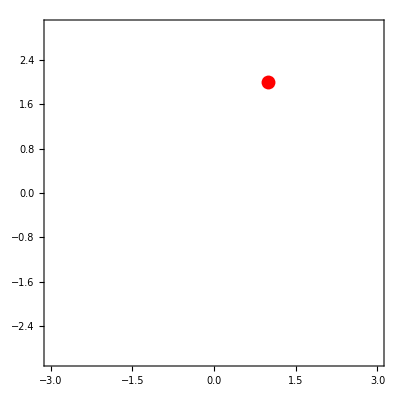

```mathematica
Range0={{-3,3},{-3,3}};
CGAOutput2D[Pnt[{1,2}] ,Range0,Axes->True,PlotStyle->{AbsolutePointSize[10],Red}]
```

```mathematica
CGAOutput3D[Pnt[{1,2,1}],{{0,3},{0,3},{0,3}},PlotStyle->{AbsolutePointSize[10],Red}]
```

-Graphics3D-

## PointPair

### 図形表示

二点{-1,-3},{2,5}∈ℝ^2

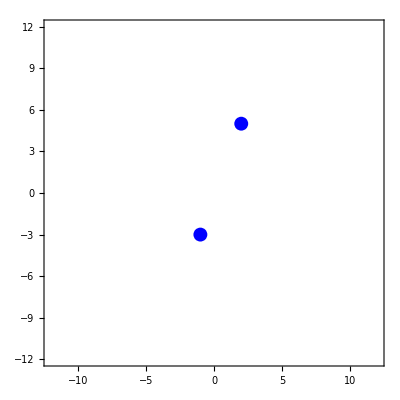

```mathematica
TestPP=Par[{-1,-3},{2,5}];
Range0={{-12,12},{-12,12}};
CGAOutput2D[TestPP,Range0,Axes->True,PlotStyle->{AbsolutePointSize[10],Blue}]
```

二点{0,0,0},{4,10,9}∈ℝ^3

```mathematica
TestPP2=Par[{0,0,0},{4,10,9}];
Range0={{-12,12},{-12,12},{-12,12}};
CGAOutput3D[TestPP2,Range0,Axes->True,PlotStyle->{AbsolutePointSize[10],Blue}]
```

-Graphics3D-

## Circle

### 図形表示

円は三点の外積で表される

三点{3,0},{0,3},{-3,0}∈ℝ^2を通る円

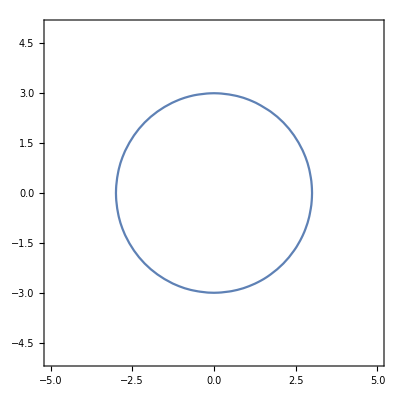

```mathematica
(*円の定義*)TestCircle=Cir[{3,0},{0,3},{-3,0}];
(*外積の係数を抜き出す*)C1=CoefPickUp[OuterProduct[TestCircle,Pnt[{x,y}]]];
(*等高線*)ContourPlot[C1==0,{x,-5,5},{y,-5,5},Axes->True]
```

三点{0,0},{2,10},{6,0}∈ℝ^2を通る円

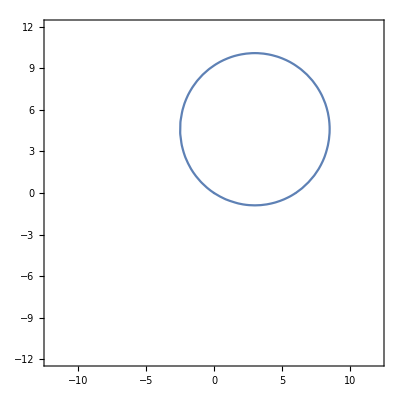

```mathematica
TestCircle2=Cir[{0,0},{2,10},{6,0}];
Range0={{-12,12},{-12,12}};
CGAOutput2D[TestCircle2 ,Range0,Axes->True]
```

三点{0,0,0},{4,10,9},{6,0,3}∈ℝ^3を通る円

```mathematica
TestCircle3=Cir[{0,0,0},{4,10,9},{6,0,3}];
Range0={{-12,12},{-12,12},{-12,12}};
CGAOutput3D[TestCircle3 ,Range0]
```

-Graphics3D-

## Sphere

### 図形表示

球は四点の外積で表される

四点{3,0,0},{0,3,0},{0,0,3},{-3,0,0}∈ℝ^3を通る球

```mathematica
TestSphere=Sph[{3,0,0},{0,3,0},{0,0,3},{-3,0,0}];
S1=CoefPickUp[OuterProduct[TestSphere,Pnt[{x,y,z}]]];
ContourPlot3D[S1==0,{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

四点{5,2,1},{3,3,3},{9,2,3},{-3,3,3}∈ℝ^3を通る球

```mathematica
TestSphere2=Sph[{5,2,1},{3,3,3},{9,2,3},{-3,11,12}];
Range0={{-40,40},{-40,40},{-40,40}};
CGAOutput3D[TestSphere2 ,Range0]
```

-Graphics3D-

## Line

### 図形表示

直線は二点と無限遠点の外積で表される. つまり三点の内の一点が無限遠にある円

二点{0,0},{2,5}∈ℝ^2を通る直線

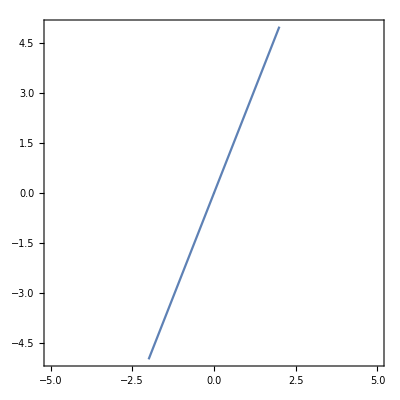

```mathematica
TestLine=Lin[{0,0},{2,5}];
L1=CoefPickUp[OuterProduct[TestLine,Pnt[{x,y}]]];
ContourPlot[L1==0,{x,-5,5},{y,-5,5},Axes->True]
```

二点{3,0},{0,3}∈ℝ^2を通る直線

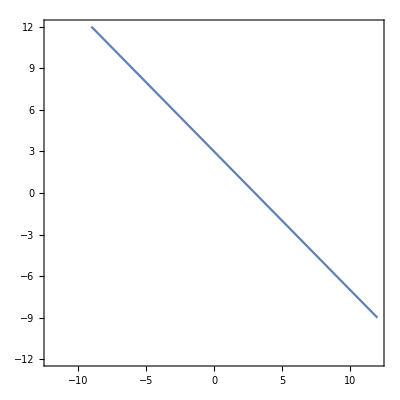

```mathematica
TestLine2=Lin[{3,0},{0,3}];
Range0={{-12,12},{-12,12}};
CGAOutput2D[TestLine2 ,Range0,Axes->True]
```

二点{0,0,0},{4,10,9}∈ℝ^3を通る直線

```mathematica
TestLine3=Lin[{0,0,0},{4,10,9}];
Range0={{-12,12},{-12,12},{-12,12}};
CGAOutput3D[TestLine3 ,Range0]
```

-Graphics3D-

## Plane

### 図形表示

平面は三点と無限遠点の外積で表される. つまり四点の内の一点が無限遠にある球

四点{3,0,1},{0,3,1},{0,2,1}∈ℝ^3を通る平面

```mathematica
TestPlane=Pln[{3,0,1},{0,3,1},{0,2,1}];
P1=CoefPickUp[OuterProduct[TestPlane,Pnt[{x,y,z}]]];
ContourPlot3D[P1==0,{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

三点{3,0,0},{0,5,4},{0,2,8}∈ℝ^3を通る平面

```mathematica
TestPlane2=Pln[{3,0,0},{0,5,4},{0,2,8}];
Range0={{-50,50},{-50,50},{-50,50}};
CGAOutput3D[TestPlane2 ,Range0]
```

-Graphics3D-

## Translator

### 計算

点P = {x, y,z} ∈ ℝ^3 のCGA上での元は,
w_0+ P + 1/2 P^2 w_∞で表される.

点{x,0}∈ℝ^2をベクトル{t,0}∈ℝ^2で平行移動

```mathematica
Pnt[{x,0}]
```

w[{0}]+x w[{1}]+1/2 x^2 w[{∞}]

```mathematica
T0=Translator[Pnt[{x,0}],Vec[{t,0}]]
```

w[{0}]+(t+x) w[{1}]+1/2 (t+x)^2 w[{∞}]

点{1,2,3}∈ℝ^3を ベクトル{t_1,t_2,t_3}∈ℝ^2で平行移動

```mathematica
Pnt[{1,2,3}]
```

w[{0}]+w[{1}]+2 w[{2}]+3 w[{3}]+7 w[{∞}]

```mathematica
Translator[Pnt[{1,2,3}],Vec[{Subscript[t, 1],Subscript[t, 2],Subscript[t, 3]}]]
```

w[{0}]+(1+t_1) w[{1}]+(2+t_2) w[{2}]+(3+t_3) w[{3}]+1/2 (14+2 t_1+t_1^2+4 t_2+t_2^2+6 t_3+t_3^2) w[{∞}]

### 図形表示

三点 {1,0},{7,0},{4,3}∈ ℝ^2 を通る円をベクトル{-8,2}∈ℝ^2で平行移動

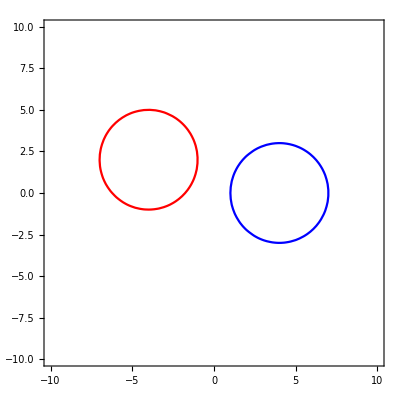

```mathematica
TestCircle=Cir[{1,0},{7,0},{4,3}];(*元の円:青色*)
TestTranslator=Translator[TestCircle,Vec[{-8,2}]];(*変換後の円:赤色*)
Range0={{-10,10},{-10,10}};
Show[
CGAOutput2D[TestCircle,Range0,Axes->True,ContourStyle->Blue],
CGAOutput2D[TestTranslator,Range0,Axes->True,ContourStyle->Red]
]
```

## Rotor

### 計算

点{1,0}∈ℝ^2をxy平面上で θ回転

```mathematica
Pnt[{1,0}]
```

w[{0}]+w[{1}]+1/2 w[{∞}]

```mathematica
R0=Rotor[Pnt[{1,0}],Biv[{1,0},{0,1}],θ]
```

w[{0}]+Cos[θ] w[{1}]+Sin[θ] w[{2}]+1/2 w[{∞}]

点{1,2,3}∈ℝ^3を xy平面上でθ回転

```mathematica
Pnt[{1,2,3}]
```

w[{0}]+w[{1}]+2 w[{2}]+3 w[{3}]+7 w[{∞}]

```mathematica
R0=Rotor[Pnt[{1,2,3}],Biv[{1,0},{0,1}],θ]
```

w[{0}]+(Cos[θ]-2 Sin[θ]) w[{1}]+(2 Cos[θ]+Sin[θ]) w[{2}]+3 w[{3}]+7 w[{∞}]

### 図形表示

三点 {1,0},{7,0},{4,3}∈ ℝ^2 を通る円をxy平面上で π/2回転

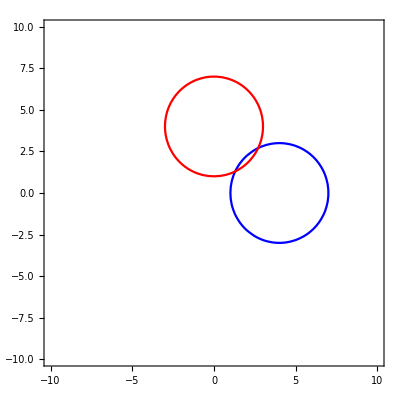

```mathematica
TestCircle=Cir[{1,0},{7,0},{4,3}];(*元の円:青色*)
TestRotor=Rotor[TestCircle,Biv[{1,0},{0,1}],π/2];(*変換後の円:赤色*)
Range0={{-10,10},{-10,10}};
Show[
CGAOutput2D[TestCircle,Range0,Axes->True,ContourStyle->Blue],
CGAOutput2D[TestRotor,Range0,Axes->True,ContourStyle->Red]
]
```

## Dilator

### 計算

点{1,2}∈ℝ^2を e^3 倍に拡大

```mathematica
Pnt[{1,2}]
```

w[{0}]+w[{1}]+2 w[{2}]+5/2 w[{∞}]

```mathematica
D0=Dilator[Pnt[{1,2}],3]
```

w[{0}]/ⅇ^3+w[{1}]+2 w[{2}]+5/2 ⅇ^3 w[{∞}]

スカラー倍は同じ元とみなせるので,w_0の係数を1にして簡約化

```mathematica
D0/Coefficient[D0,w[{0}]]//Expand
```

w[{0}]+ⅇ^3 w[{1}]+2 ⅇ^3 w[{2}]+5/2 ⅇ^6 w[{∞}]

```mathematica
NPnt[D0]
```

w[{0}]+ⅇ^3 w[{1}]+2 ⅇ^3 w[{2}]+5/2 ⅇ^6 w[{∞}]

### 図形表示

三点{3,0},{0,3},{-3,0}∈ℝ^2を通る円をe^2 倍に拡大

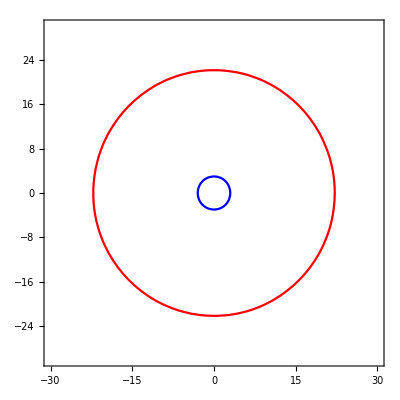

```mathematica
TestCircle=Cir[{3,0},{0,3},{-3,0}];(*元の円:青色*)
TestDilator=Dilator[TestCircle,2];(*変換後の円:赤色*)
Range0={{-30,30},{-30,30}};
Show[
CGAOutput2D[TestCircle,Range0,Axes->True,ContourStyle->Blue],
CGAOutput2D[TestDilator,Range0,Axes->True,ContourStyle->Red]
]
```

```mathematica
TestCircle=Cir[{3,0},{0,3},{-3,0}];(*元の円:青色*)
TestDilator=Dilator[TestCircle,2];(*変換後の円:赤色*)
Range0={{-30,30},{-30,30}};
Show[
CGAOutput2D[TestCircle,Range0,Axes->True,ContourStyle->Blue],
CGAOutput2D[TestDilator,Range0,Axes->True,ContourStyle->Red]
]
```

三点{30,0},{0,30},{-30,0}∈ℝ^2を通る円をe^-1 倍に縮小

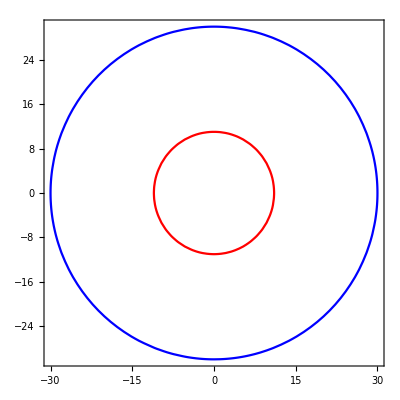

```mathematica
TestCircle2=Cir[{30,0},{0,30},{-30,0}];(*元の円:青色*)
TestDilator2=Dilator[TestCircle2,-1];(*変換後の円:赤色*)
Range0={{-30,30},{-30,30}};
Show[
CGAOutput2D[TestCircle2,Range0,Axes->True,ContourStyle->Blue],
CGAOutput2D[TestDilator2,Range0,Axes->True,ContourStyle->Red]
]
```

## CGAOutput

CGAの元をユークリッド空間上に表示する.

### CGAOutput2D

CGAOutput2D は,二次元空間にプロットする関数である.
引数には,CGAの元と表示する範囲を用いる.

```mathematica
TestCircle2=Cir[{0,0},{2,10},{6,0}];
Range0={{-12,12},{-12,12}};
CGAOutput2D[TestCircle2 ,Range0,Axes->True]
```

-Graphics-

### CGAOutput3D

CGAOutput3D は,三次元空間にプロットする関数である.
引数には,CGAの元と表示する範囲を用いる.

#### 連立方程式１つ

3次元上の物体,面,球 → ContourPlot3Dで等高面を表示

[例]  x^2+y^2+z^2-1=0

```mathematica
TestSphere=Sph[{3,0,0},{0,3,1},{0,2,3},{-3,3,2}];
OuterProduct[TestSphere,Pnt[{x,y,z}]]
CGAOutput3D[TestSphere,{{-10,10},{-10,10},{-10,10}}]
```

(-37 x-3 (-64+11 y+z)-9 (x^2+y^2+z^2)) w[{0,1,2,3,∞}]

-Graphics3D-

#### 連立方程式２つ

2次元の物体,直線,円 →ParametricPlot3Dで{x,y,z}の内一つをパラメータとして表示

[例]  x-z-1=0, y+z-3=0  
→{x,y,z}={z+1,-z+3,z}

```mathematica
TestLine=Lin[{0,3,0},{2,5,4}];
OuterProduct[TestLine,Pnt[{x,y,z}]]
CGAOutput3D[TestLine ,{{-5,5},{-5,5},{-5,5}}]
```

2 (3+x-y) w[{0,1,2,∞}]+(4 x-2 z) w[{0,1,3,∞}]+(4 y-2 (6+z)) w[{0,2,3,∞}]+6 (-2 x+z) w[{1,2,3,∞}]

-Graphics3D-

#### 連立方程式３つ

1次元の物体,点 → ListPointPlot3Dで点を表示

[例]  x^2-1=0, y-3=0  , z+4=0 
→{x,y,z}={1,3,-4}, {-1,3,-4}

```mathematica
TestPointPair=OuterProduct[Pnt[{3,2,0}],Pnt[{0,4,0}]];
OuterProduct[TestPointPair,Pnt[{x,y,z}]]
CGAOutput3D[TestPointPair,{{-5,5},{-5,5},{-5,5}}]
```

(12-2 x-3 y) w[{0,1,2}]-3 z w[{0,1,3}]-3/2 (-16+x+x^2+y^2+z^2) w[{0,1,∞}]+2 z w[{0,2,3}]+(-10+x^2-(3 y)/2+y^2+z^2) w[{0,2,∞}]-3/2 z w[{0,3,∞}]+12 z w[{1,2,3}]+(-10 x+6 x^2+6 (-4 y+y^2+z^2)) w[{1,2,∞}]-24 z w[{1,3,∞}]+10 z w[{2,3,∞}]

-Graphics3D-

## SegOutput

線分をユークリッド空間上に表示する.

### SegOutput2D

SegOutput2D は,二次元空間にプロットする関数である.
引数には,CGAの点を二つ用いる.

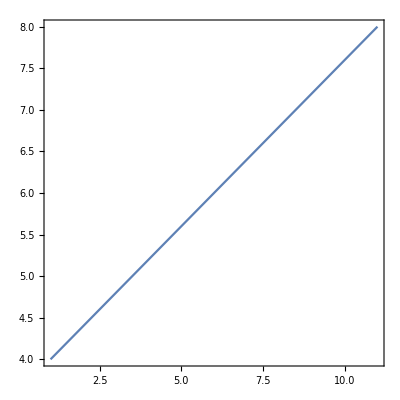

```mathematica
SegOutput2D[Pnt[{1,4}],Pnt[{11,8}]]
```

### SegOutput3D

SegOutput3D は,三次元空間にプロットする関数である.
引数には,CGAの点を二つ用いる.

入力された二点間の線分を表示.

```mathematica
SegOutput3D[Pnt[{5,0,4}],Pnt[{11,8,4}]]
```

-Graphics3D-

### 面白い例

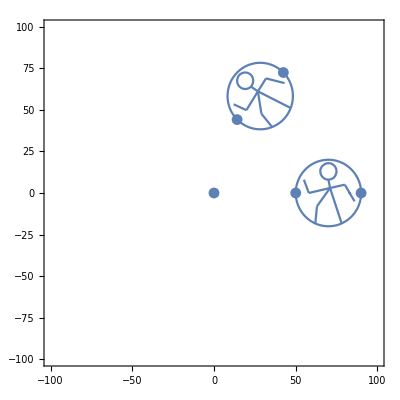

```mathematica
i=50;
TestPoint1=Pnt[{50,0}];TestPoint2=Pnt[{90,0}];
TestCircle1=Cir[{50,0},{90,0},{70,20}];
TestCircle2=Cir[{65,13},{75,13},{70,18}];

SPoint1=Pnt[{70,8}];
SPoint2=Pnt[{71,3}];
SPoint3=Pnt[{58,0}];
SPoint4=Pnt[{55,8}];
SPoint5=Pnt[{80,5}];
SPoint6=Pnt[{86,-5}];
SPoint7=Pnt[{78,-18}];
SPoint8=Pnt[{63,-8}];
SPoint9=Pnt[{62,-18}];

FVec=Vec[{-30,30}];FBiv=Biv[{1,0},{0,1}];

TestFP1=F[TestPoint1,FVec,FBiv,π/2,i/100];
TestFP2=F[TestPoint2,FVec,FBiv,π/2,i/100];
TestFC1=F[TestCircle1,FVec,FBiv,π/2,i/100];
TestFC2=F[TestCircle2,FVec,FBiv,π/2,i/100];

TestFSP1=F[SPoint1,FVec,FBiv,π/2,i/100];
TestFSP2=F[SPoint2,FVec,FBiv,π/2,i/100];
TestFSP3=F[SPoint3,FVec,FBiv,π/2,i/100];
TestFSP4=F[SPoint4,FVec,FBiv,π/2,i/100];
TestFSP5=F[SPoint5,FVec,FBiv,π/2,i/100];
TestFSP6=F[SPoint6,FVec,FBiv,π/2,i/100];
TestFSP7=F[SPoint7,FVec,FBiv,π/2,i/100];
TestFSP8=F[SPoint8,FVec,FBiv,π/2,i/100];
TestFSP9=F[SPoint9,FVec,FBiv,π/2,i/100];

Range1 ={{-100,100},{-100,100}};
Show[CGAOutput2D[Pnt[{0,0}],Range1 ],

SegOutput2D[SPoint1,SPoint2],
SegOutput2D[SPoint2,SPoint3],
SegOutput2D[SPoint3,SPoint4],
SegOutput2D[SPoint2,SPoint5],
SegOutput2D[SPoint5,SPoint6],
SegOutput2D[SPoint2,SPoint7],
SegOutput2D[SPoint2,SPoint8],
SegOutput2D[SPoint8,SPoint9],

SegOutput2D[TestFSP1,TestFSP2],
SegOutput2D[TestFSP2,TestFSP3],
SegOutput2D[TestFSP3,TestFSP4],
SegOutput2D[TestFSP2,TestFSP5],
SegOutput2D[TestFSP5,TestFSP6],
SegOutput2D[TestFSP2,TestFSP7],
SegOutput2D[TestFSP2,TestFSP8],
SegOutput2D[TestFSP8,TestFSP9],

CGAOutput2D[TestPoint1,Range1 ],
CGAOutput2D[TestPoint2,Range1 ],
CGAOutput2D[TestCircle1,Range1] ,
CGAOutput2D[TestCircle2,Range1] ,

CGAOutput2D[TestFP1,Range1],
CGAOutput2D[TestFP2,Range1] ,
CGAOutput2D[TestFC1,Range1] ,
CGAOutput2D[TestFC2,Range1] 
]
```

## 第三章 応用例

## 交点-CGAIntersection-

CGAの元の交点を調べる.

CGAIntersection は,交点を調べる関数である.
引数には,CGAの元を二つ用いる.

### 計算

```mathematica
TestLine=Lin[{3,4,0},{3,4,1}];
TestPlane=Pln[{3,0,1},{0,3,1},{0,2,1}];
CGAIntersection[TestLine,TestPlane]
```

{{3,4,1}}

```mathematica
TestPointPair=Par[{4,2,3},{2,3,4}];
TestPlane=Pln[{4,2,3},{2,3,4},{0,2,8}];
CGAIntersection[TestPointPair,TestPlane]
```

{{2,3,4},{4,2,3}}

```mathematica
TestCircle=Cir[{1,0,2},{7,0,3},{4,3,5}];
TestPlane=Pln[{4,2,3},{2,3,4},{0,2,8}];
CGAIntersection[TestCircle,TestPlane]
Show[CGAOutput3D[TestCircle,{{-10,10},{-10,10},{-10,10}}],CGAOutput3D[TestPlane,{{-10,10},{-10,10},{-10,10}}]]
```

{{(2 (10447+14 √163681))/4653,(5594-17 √163681)/4653,(33349-19 √163681)/9306},{(2 (10447-14 √163681))/4653,(5594+17 √163681)/4653,(33349+19 √163681)/9306}}

-Graphics3D-

交点が無いときは虚数がでる

```mathematica
TestCircle=Cir[{1,0,2},{7,0,3},{4,3,5}];
TestCircle=Translator[TestCircle,Vec[{-3,-3,-3}]];
TestPlane=Pln[{4,2,3},{2,3,4},{0,2,8}];
CGAIntersection[TestCircle,TestPlane]
Show[CGAOutput3D[TestCircle,{{-10,10},{-10,10},{-10,10}}],CGAOutput3D[TestPlane,{{-10,10},{-10,10},{-10,10}}]]
```

{{(2 (10195+14 ⅈ √536879))/4653,(5900-17 ⅈ √536879)/4653,(33691-19 ⅈ √536879)/9306},{(2 (10195-14 ⅈ √536879))/4653,(5900+17 ⅈ √536879)/4653,(33691+19 ⅈ √536879)/9306}}

-Graphics3D-

### Dual

片方Dualの内積は交点となる

```mathematica
TestCircle=Cir[{1,0,2},{7,0,3},{4,3,5}];
TestPlane=Pln[{4,2,3},{2,3,4},{0,2,8}];
I0=CGAIntersection[TestCircle,TestPlane]
```

{{(2 (10447+14 √163681))/4653,(5594-17 √163681)/4653,(33349-19 √163681)/9306},{(2 (10447-14 √163681))/4653,(5594+17 √163681)/4653,(33349+19 √163681)/9306}}

```mathematica
dual0=Dual[TestCircle];
C0=InnerProduct[TestPlane,dual0];
CGAIntersection[TestCircle,C0]
```

{{(2 (10447+14 √163681))/4653,(5594-17 √163681)/4653,(33349-19 √163681)/9306},{(2 (10447-14 √163681))/4653,(5594+17 √163681)/4653,(33349+19 √163681)/9306}}

```mathematica
Range0={{-10,10},{-10,10},{-10,10}};
Show[CGAOutput3D[TestCircle,Range0],
CGAOutput3D[TestPlane,Range0],
CGAOutput3D[C0,Range0]
]
CGAOutput3D[C0,Range0]
```

-Graphics3D-

-Graphics3D-

```mathematica
TestCircle=Cir[{1,0,2},{7,0,3},{4,3,5}];
TestPlane=Pln[{4,2,3},{2,3,4},{0,2,8}];
I0=CGAIntersection[TestCircle,TestPlane];
P0=Par[I0[[1]],I0[[2]]]

dual0=Dual[TestCircle];
C0=InnerProduct[TestPlane,dual0]

CGAEquationCheck[P0,C0]
```

-(56 √163681 w[{0,1}])/4653+(34 √163681 w[{0,2}])/4653+(19 √163681 w[{0,3}])/4653-(95 √163681 w[{0,∞}])/3102+20/423 √163681 w[{1,2}]+26/423 √163681 w[{1,3}]+(571 √163681 w[{1,∞}])/4653-1/47 √163681 w[{2,3}]-(1813 √163681 w[{2,∞}])/9306-(1843 √163681 w[{3,∞}])/9306

-168 w[{0,1}]+102 w[{0,2}]+57 w[{0,3}]-855/2 w[{0,∞}]+660 w[{1,2}]+858 w[{1,3}]+1713 w[{1,∞}]-297 w[{2,3}]-5439/2 w[{2,∞}]-5529/2 w[{3,∞}]

True

## CGAEquationCheck

CGAの元がユークリッド空間上で一致するか調べる.

CGAEquationCheck は,同値判定を表す関数である.
引数には,CGAの元の組を用いる.

### 計算例

```mathematica
TestCircle=Cir[{1,0,2},{7,0,3},{4,3,5}];
CGAEquationCheck[TestCircle,CGAProduct[TestCircle,Sca[2]]]
```

True

```mathematica
TestSphere=Sph[{3,0,0},{0,3,0},{0,0,3},{-3,0,0}];
CGAEquationCheck[TestSphere,CGAProduct[TestCircle,Sca[2]]]
```

False

```mathematica
A1=2 w[{0,1,2}]+4 w[{0,1,3}]+11 w[{0,1,∞}]+2 w[{0,2,3}]+22 w[{0,2,∞}]+33 w[{0,3,∞}]+14 w[{1,2,∞}]+28 w[{1,3,∞}]+14 w[{2,3,∞}]+6 w[{0,1,2,3}]+44 w[{0,1,2,∞}]+55 w[{0,1,3,∞}]+66 w[{0,2,3,∞}]+46 w[{1,2,3,∞}];
A2=w[{0,2}]+2 w[{0,3}]+11/2 w[{0,∞}]+w[{1,2}]+2 w[{1,3}]+11/2 w[{1,∞}]+w[{2,3}]+4 w[{2,∞}]+5/2 w[{3,∞}];
CGAEquationCheck[A1,A2]
```

True

### 図

```mathematica
CGAOutput3D[2 w[{0,1,2}]+4 w[{0,1,3}]+11 w[{0,1,∞}]+2 w[{0,2,3}]+22 w[{0,2,∞}]+33 w[{0,3,∞}]+14 w[{1,2,∞}]+28 w[{1,3,∞}]+14 w[{2,3,∞}]+6 w[{0,1,2,3}]+44 w[{0,1,2,∞}]+55 w[{0,1,3,∞}]+66 w[{0,2,3,∞}]+46 w[{1,2,3,∞}],{{0,2},{0,3},{0,4}},PlotStyle->{PointSize[0.02],Blue}]
```

-Graphics3D-

```mathematica
Par[{1,1,1},{1,2,3}]
```

w[{0,2}]+2 w[{0,3}]+11/2 w[{0,∞}]+w[{1,2}]+2 w[{1,3}]+11/2 w[{1,∞}]+w[{2,3}]+4 w[{2,∞}]+5/2 w[{3,∞}]

```mathematica
CGAOutput3D[w[{0,2}]+2 w[{0,3}]+11/2 w[{0,∞}]+w[{1,2}]+2 w[{1,3}]+11/2 w[{1,∞}]+w[{2,3}]+4 w[{2,∞}]+5/2 w[{3,∞}],{{0,2},{0,3},{0,4}},PlotStyle->{PointSize[0.02],Red}]
```

-Graphics3D-